## sigma

```mathematica
Clear[sig,s,μ,B,v0];
sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,s,sm=0,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;
kf1[θ_]=μ/v0;(* -Graphics-*);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];

h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=3/2;
kf2[θ_]=μ/v0;
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=s v0 kf2[θ];
h2[θ_]=1/Dphase2[θ]( s v0 Cos[θ]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])) );

(* ***************************** *)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]
(*********** (3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(**************) 

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]+

(*****(3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3 ***************************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2,s1+s2(*,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol0],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol1],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol2]*)}
];
(* sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
	(*mu=10.0^-1;v0val= 6 10^-4;in=1;
	Quiet[sig[0.01,mu,v0val,{in,in,0.5 in}]]
	Quiet[sig[-0.01,mu,v0val,{in,in,0.5 in}]]
	Quiet[sig[0.00000001,mu,v0val,{in,in,0.5 in}]]
Quiet[sig0[mu,v0val,{in,in,0.5 in}]]*)
```

## sigma at B=0

```mathematica
Clear[sig0,s,μ,B,v0];
sig0[μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,B=0,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ] );
(*****************)

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=μ/v0;
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 ;
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=v0 s kf2[θ];
h2[θ_]=(s v0 Cos[θ])/Dphase2[θ];

(* ***************************** *)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]
(*********** (3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(**************) 

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}]+

(*****(3+3 ctp^2)+ct(-3 ctp+9 ctp^3) +(3-9 ctp^2) ct^2+(9 ctp-15 ctp^3) ct^3 ***************************)+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1+ Cos[θp]^2),{θp,0,π}]+(-3βinter Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (1-3 Cos[θp]^2),{θp,0,π}]+(3βinter Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](1-3 Cos[θp]^2) ,{θp,0,π}]+(3βinter Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](3 -5 Cos[θp]^2) ,{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,(*matr[[3]]+colvec[[3]]==0,*)matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2,s1+s2(*,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol0],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol1],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol2]*)}
];
(* sig0[μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
(*mu=10.0^-1;v0val= 6 10^-4;in=1;
Quiet[sig0[mu,v0val,{in,in,0.5 in}]]*)
```

## data

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.5;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
```

{0,7.93269×10^-9,3.67788×10^-8,4.47115×10^-8}

```mathematica
list={{-105,7.932311914240743*^-9,3.678038571367491*^-8,4.471269762791565*^-8},{-95,7.932380919847297*^-9,3.678010642711565*^-8,4.471248734696295*^-8},{-85,7.93244302489631*^-9,3.677985506971616*^-8,4.471229809461247*^-8},{-75,7.932498229386813*^-9,3.67796316413173*^-8,4.471212987070411*^-8},{-65,7.932546533317924*^-9,3.6779436141777686*^-8,4.4711982675095606*^-8},{-55,7.93258793668887*^-9,3.677926857097352*^-8,4.471185650766239*^-8},{-45,7.932622439499*^-9,3.67791289287988*^-8,4.47117513682978*^-8},{-35,7.932650041747752*^-9,3.677901721516505*^-8,4.47116672569128*^-8},{-25,7.932670743434706*^-9,3.677893343000163*^-8,4.471160417343634*^-8},{-15,7.932684544559524*^-9,3.677887757325548*^-8,4.4711562117815*^-8},{-5,7.93269144512199*^-9,3.677884964489124*^-8,4.4711541090013225*^-8},{0,7.932692307692297*^-9,3.6778846153846116*^-8,4.4711538461538415*^-8},{5,7.932691445121991*^-9,3.677884964489123*^-8,4.4711541090013225*^-8},{15,7.932684544559527*^-9,3.677887757325547*^-8,4.4711562117815*^-8},{25,7.932670743434708*^-9,3.677893343000164*^-8,4.4711604173436345*^-8},{35,7.932650041747752*^-9,3.677901721516506*^-8,4.4711667256912815*^-8},{45,7.932622439498994*^-9,3.6779128928798794*^-8,4.471175136829779*^-8},{55,7.93258793668887*^-9,3.677926857097352*^-8,4.471185650766239*^-8},{65,7.932546533317925*^-9,3.6779436141777686*^-8,4.471198267509561*^-8},{75,7.932498229386813*^-9,3.67796316413173*^-8,4.471212987070411*^-8},{85,7.93244302489631*^-9,3.677985506971615*^-8,4.471229809461246*^-8},{95,7.93238091984729*^-9,3.678010642711565*^-8,4.471248734696294*^-8},{105,7.932311914240741*^-9,3.67803857136749*^-8,4.471269762791564*^-8}};
len=Length[list];
{x1,x2}={1/7.932692307692297*^-9,1/3.6778846153846116*^-8};
dat11=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat12=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat11];
ListLinePlot[dat12];
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=1;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
```

{0,7.03125×10^-9,2.10937×10^-8,2.8125×10^-8}

```mathematica
list={{-105,7.031053288928242*^-9,2.1094408856623247*^-8,2.812546214555149*^-8},{-95,7.031088973474902*^-9,2.1094289335389445*^-8,2.8125378308864347*^-8},{-85,7.031121089567465*^-9,2.1094181766566255*^-8,2.812530285613372*^-8},{-75,7.031149637205752*^-9,2.1094086150062942*^-8,2.8125235787268692*^-8},{-65,7.031174616389607*^-9,2.10940024857989*^-8,2.8125177102188505*^-8},{-55,7.03119602711888*^-9,2.10939307737036*^-8,2.812512680082248*^-8},{-45,7.031213869393462*^-9,2.1093871013716546*^-8,2.812508488311001*^-8},{-35,7.031228143213241*^-9,2.1093823205787373*^-8,2.8125051349000615*^-8},{-25,7.03123884857815*^-9,2.1093787349875772*^-8,2.812502619845392*^-8},{-15,7.031245985488122*^-9,2.1093763445951485*^-8,2.8125009431439608*^-8},{-5,7.0312495539431166*^-9,2.109375149399439*^-8,2.8125001047937504*^-8},{0,7.031249999999994*^-9,2.1093749999999977*^-8,2.812499999999997*^-8},{5,7.031249553943119*^-9,2.1093751493994386*^-8,2.8125001047937504*^-8},{15,7.031245985488123*^-9,2.1093763445951492*^-8,2.8125009431439615*^-8},{25,7.031238848578152*^-9,2.1093787349875762*^-8,2.8125026198453914*^-8},{35,7.031228143213243*^-9,2.1093823205787373*^-8,2.8125051349000615*^-8},{45,7.0312138693934585*^-9,2.1093871013716546*^-8,2.8125084883110005*^-8},{55,7.0311960271188805*^-9,2.109393077370359*^-8,2.812512680082247*^-8},{65,7.031174616389606*^-9,2.1094002485798903*^-8,2.812517710218851*^-8},{75,7.031149637205753*^-9,2.109408615006294*^-8,2.8125235787268692*^-8},{85,7.031121089567465*^-9,2.1094181766566248*^-8,2.8125302856133713*^-8},{95,7.031088973474901*^-9,2.1094289335389455*^-8,2.8125378308864354*^-8},{105,7.031053288928241*^-9,2.1094408856623247*^-8,2.812546214555149*^-8}};
len=Length[list];
{x1,x2}={1/7.031249999999994*^-9,1/2.1093749999999977*^-8};
dat21=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat22=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat21];
ListLinePlot[dat22];
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=2;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
```

{0,5.65476×10^-9,1.16071×10^-8,1.72619×10^-8}

```mathematica
list=(*Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-105,105,10}]]]*){{-105,5.654663178400109*^-9,1.160743434599545*^-8,1.7262097524395557*^-8},{-95,5.6546810879468784*^-9,1.1607381467789372*^-8,1.726206255573625*^-8},{-85,5.654697206537955*^-9,1.1607333877559156*^-8,1.726203108409711*^-8},{-75,5.654711534173658*^-9,1.1607291575255768*^-8,1.7262003109429428*^-8},{-65,5.654724070854276*^-9,1.1607254560835633*^-8,1.7261978631689907*^-8},{-55,5.654734816580058*^-9,1.160722283426062*^-8,1.7261957650840677*^-8},{-45,5.654743771351215*^-9,1.1607196395498044*^-8,1.7261940166849258*^-8},{-35,5.654750935167928*^-9,1.1607175244520663*^-8,1.7261926179688592*^-8},{-25,5.654756308030336*^-9,1.1607159381306693*^-8,1.7261915689337027*^-8},{-15,5.654759889938551*^-9,1.1607148805839791*^-8,1.7261908695778343*^-8},{-5,5.654761680892642*^-9,1.1607143518109064*^-8,1.7261905199001704*^-8},{0,5.654761904761898*^-9,1.1607142857142846*^-8,1.7261904761904745*^-8},{5,5.6547616808926425*^-9,1.1607143518109065*^-8,1.7261905199001708*^-8},{15,5.654759889938552*^-9,1.1607148805839793*^-8,1.7261908695778343*^-8},{25,5.654756308030339*^-9,1.160715938130669*^-8,1.7261915689337027*^-8},{35,5.654750935167926*^-9,1.1607175244520664*^-8,1.7261926179688592*^-8},{45,5.654743771351214*^-9,1.1607196395498044*^-8,1.7261940166849258*^-8},{55,5.654734816580058*^-9,1.1607222834260617*^-8,1.7261957650840677*^-8},{65,5.654724070854278*^-9,1.1607254560835636*^-8,1.7261978631689914*^-8},{75,5.654711534173659*^-9,1.160729157525577*^-8,1.7262003109429428*^-8},{85,5.654697206537954*^-9,1.1607333877559157*^-8,1.726203108409711*^-8},{95,5.6546810879468784*^-9,1.1607381467789375*^-8,1.7262062555736255*^-8},{105,5.65466317840011*^-9,1.160743434599545*^-8,1.726209752439556*^-8}};
len=Length[list];
{x1,x2}={1/5.654761904761898*^-9,1/1.1607142857142846*^-8};
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat32=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat31];
ListLinePlot[dat32];
```

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.1;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
(*list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-105,105,10}]]]*)
```

{0,8.42863×10^-9,9.7151×10^-8,1.0558×10^-7}

```mathematica
list={{-105,8.426820505364826*^-9,9.716266122607005*^-8,1.0558948173143487*^-7},{-95,8.427148351958018*^-9,9.716055038590418*^-8,1.0558769873786219*^-7},{-85,8.427443413929191*^-9,9.715865063091926*^-8,1.0558609404484845*^-7},{-75,8.42770569126656*^-9,9.715696196074756*^-8,1.0558466765201412*^-7},{-65,8.427935183959665*^-9,9.715548437506216*^-8,1.0558341955902182*^-7},{-55,8.42813189199933*^-9,9.715421787357731*^-8,1.0558234976557664*^-7},{-45,8.428295815377724*^-9,9.715316245604774*^-8,1.0558145827142547*^-7},{-35,8.428426954088281*^-9,9.715231812226911*^-8,1.055807450763574*^-7},{-25,8.428525308125784*^-9,9.715168487207819*^-8,1.0558021018020397*^-7},{-15,8.4285908774863*^-9,9.715126270535225*^-8,1.0557985358283855*^-7},{-5,8.428623662167214*^-9,9.715105162200981*^-8,1.0557967528417702*^-7},{0,8.428627760252351*^-9,9.715102523659288*^-8,1.0557965299684523*^-7},{5,8.428623662167215*^-9,9.715105162200977*^-8,1.0557967528417698*^-7},{15,8.4285908774863*^-9,9.715126270535232*^-8,1.0557985358283863*^-7},{25,8.428525308125787*^-9,9.715168487207816*^-8,1.0558021018020395*^-7},{35,8.428426954088281*^-9,9.71523181222691*^-8,1.0558074507635737*^-7},{45,8.428295815377719*^-9,9.715316245604773*^-8,1.0558145827142545*^-7},{55,8.428131891999332*^-9,9.715421787357731*^-8,1.0558234976557664*^-7},{65,8.42793518395966*^-9,9.715548437506224*^-8,1.055834195590219*^-7},{75,8.42770569126656*^-9,9.715696196074756*^-8,1.0558466765201412*^-7},{85,8.427443413929191*^-9,9.715865063091924*^-8,1.0558609404484844*^-7},{95,8.427148351958016*^-9,9.716055038590418*^-8,1.0558769873786219*^-7},{105,8.426820505364824*^-9,9.716266122607005*^-8,1.0558948173143487*^-7}};
len=Length[list];
{x1,x2}={1/8.428627760252351*^-9,1/9.715102523659288*^-8};
dat01=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat02=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat01];
ListLinePlot[dat02];
```

## Plots

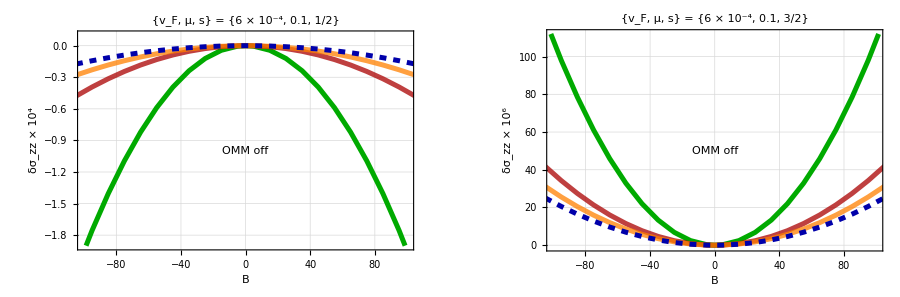

```mathematica
style={(**)Directive[Darker[Green],Thickness[0.008]],(**)Directive[Darker[Red],Thickness[0.008],Opacity[0.75]],(**)Directive[Orange,Thickness[0.008],Opacity[0.75]](*********),(**)Directive[Darker[Blue],Thickness[0.008],Dashed]};

g1=ListPlot[{dat01,dat11,dat21,dat31},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-1.9,0.1}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^4"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 1/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["OMM off",{0,-1}],Blue,16,Bold,FontFamily->"Times"]}(*******)];

g2=ListPlot[{dat02,dat12,dat22,dat32},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.8,112}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^6"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 3/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["OMM off",{0,50}],Blue,16,Bold,FontFamily->"Times"]}(*******)];

leg=LineLegend[style,{"{1, 1, 0.1}", "{1, 1, 0.5}", "{1, 1, 1}", "{1, 1, 2}"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2}},Spacings->{40,0},ImageSize->900],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["allnoomm.pdf",Rasterize[pl],ImageResolution->1000];
```